## Визуализация результатов Лабораторной работы №1

### 1. Маятник

Sin[t]

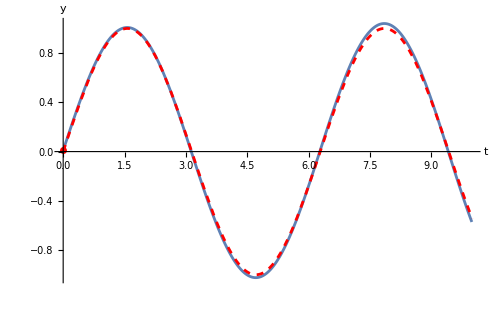

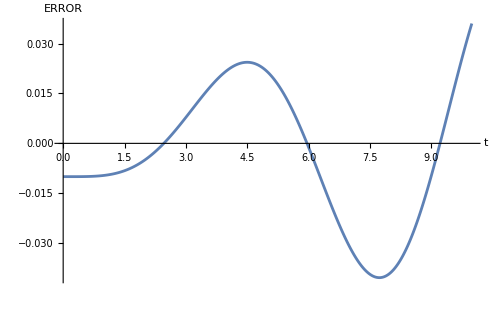

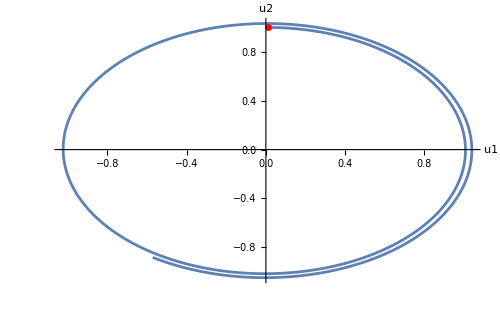

```mathematica
m = 1; k = 1; 
u10=0;u20=1;
solve1 = DSolve[{y''[t]+k/m y[t]==0,y[0]==u10,y'[0]==u20},y[t],t][[1]][[1]][[2]]
plotsolve1= Plot[solve1,{t,0,10},PlotStyle->{Red,Dashed}];
data1=Import["C:\\Users\\gerce\\WORK DIRECTORY\\NumericalMethods\\Semester_2\\Code_lab_1\\data\\data1.txt","Table"];
plot1data1= ListPlot[Table[{data1[[i]][[1]],data1[[i]][[2]]},{i,1,Length[data1]}],Joined->True];
Show[plot1data1, Graphics[{Red,PointSize[0.01],Point[{data1[[1]][[1]],data1[[1]][[2]]}]}],
 plotsolve1,AxesLabel->{"t", "y"},AxesStyle->Arrowheads[0.03],ImageSize->500]
plot2data1=ListPlot[Table[{data1[[i]][[2]],data1[[i]][[3]]},{i,1,Length[data1]}],Joined->True,AxesLabel->{"u1", "u2"}];
ploterror1 = ListPlot[Table[{data1[[i]][[1]], (solve1/.t->data1[[i]][[1]])-data1[[i]][[2]]}, {i,1,Length[data1]}], Joined->True,AxesLabel->{"t", "ERROR"}]
Show[plot2data1,Graphics[{Red,PointSize[0.01],Point[{data1[[1]][[2]],data1[[1]][[3]]}]}],(*RegionPlot[x^2/2+(k/m y^2)/2<=m u20^2/2+(k u10^2)/2,{x,-1,1},{y,-1,1},BoundaryStyle->{Dashed,Pink},PlotStyle->Opacity[0]],*) AxesStyle->Arrowheads[0.03],ImageSize->500]
```